## Supporting calculations for the exponential growth model

#### Compute t_2 from the equation for chi

```mathematica
Solve[x==Exp[rm*t2]/(Exp[rm*t2]+Exp[rwt*(t1+t2)]) && x<1,t2,Reals]
```

{{t2→ConditionalExpression[(rwt t1-Log[(1-x)/x])/(rm-rwt), 0<x<1]}}

#### Compute the integral for the conditional sweep probability

```mathematica
Integrate[Exp[r*(t1+tau)],{tau,0,t2}]
```

(ⅇ^(r t1) (-1+ⅇ^(r t2)))/r

```mathematica
FullSimplify[(ⅇ^(r t1) (-1+ⅇ^(r t2)))/r]
```

(ⅇ^(r t1) (-1+ⅇ^(r t2)))/r

Now, calculate the unconditional sweep probability from here

```mathematica
lambda[mu_,rwt_,rm_,x_,t1_]:=mu*(ⅇ^(rwt t1) (-1+ⅇ^(rwt*((rwt t1-Log[(1-x)/x])/(rm-rwt)))))/rwt
```

```mathematica
fT[mu_,t_,rwt_]:=mu/rwt*Exp[-mu/rwt*Exp[rwt*t]]
fT2[mu_,t_,rwt_]:=mu*Exp[rwt*t]*Exp[-mu/rwt*Exp[rwt*t]]
```

```mathematica
CondSweep[mu_,rwt_,rm_,x_,t1_]:=Exp[-lambda[mu,rwt,rm,x,t1]]
```

#### From here, we can compute the conditional sweep probability numerically

```mathematica
NIntegrate[CondSweep[10^-6,1.0,2.0,0.99,t]*fT[10^-6,t,1.0],{t,0,Infinity}]
```

4.32164×10^-6

```mathematica
mu=10^-6
```

1/1000000

#### Let us plot the conditional sweep probability for some parameter values

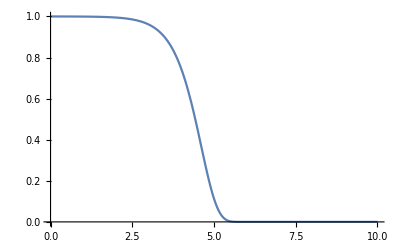

```mathematica
Plot[CondSweep[10^-6,1.0,2.0,0.99,t],{t,0,10}]
```

#### The unconditional sweep probability can be further evaluated

```mathematica
Integrate[CondSweep[u,rwt,rm,x,t]*fT[u,t,rwt],t]
```

((rm-rwt) u ExpIntegralEi[-(ⅇ^((rm rwt t)/(rm-rwt)) u (-1+1/x)^(-rwt/(rm-rwt)))/rwt])/(rm rwt^2)

```mathematica
FullSimplify[((rm-rwt) u ExpIntegralEi[-(ⅇ^((rm rwt t)/(rm-rwt)) u (-1+1/x)^(-rwt/(rm-rwt)))/rwt])/(rm rwt^2)]
```

```mathematica
Bound[u_,rwt_,rm_,x_,t_]:=((rm-rwt) u ExpIntegralEi[-(ⅇ^((rm rwt t)/(rm-rwt)) u (-1+1/x)^(-rwt/(rm-rwt)))/rwt])/(rm rwt^2)
```

```mathematica
Bound[u,rwt,rm,x,0]
```

((rm-rwt) u ExpIntegralEi[-(u (-1+1/x)^(-rwt/(rm-rwt)))/rwt])/(rm rwt^2)

```mathematica
Bound[u,rwt,rm,x,Infinity]
```

((rm-rwt) u ExpIntegralEi[-(ⅇ^((rm rwt ∞)/(rm-rwt)) u (-1+1/x)^(-rwt/(rm-rwt)))/rwt])/(rm rwt^2)

```mathematica
ExpIntegralEi[-Infinity]
```

0

```mathematica
Sweep[rwt_,rm_,u_,x_]:=-((rm-rwt) u ExpIntegralEi[-(u (-1+1/x)^(-rwt/(rm-rwt)))/rwt])/(rm rwt^2)
```

```mathematica
Sweep[1.0,2.0,10^-5,0.99]
```

0.0000317079

General::unfl: Underflow occurred in computation.

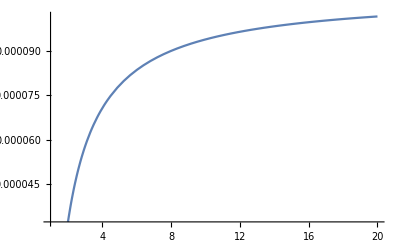

```mathematica
Plot[Sweep[1.0,rm,10^(-5),0.99],{rm,1.0,20.0}]
```

```mathematica
Integrate[Exp[r*t1],{t1,0,t}]
```

(-1+ⅇ^(r t))/r

```mathematica
Integrate[CondSweep[u,rwt,rm,x,t]*fT2[u,t,rwt],{t,0,Infinity}]
```

∫_0^∞ ⅇ^(rwt t-(ⅇ^(rwt t) u)/rwt-(ⅇ^(rwt t) (-1+ⅇ^((rwt (rwt t-Log[(1-x)/x]))/(rm-rwt))) u)/rwt) uⅆt

```mathematica
Integrate[CondSweep[10^(-5),1.0,2.0,0.99,t]*fT2[10^-5,t,1.0],{t,0,Infinity}]
```

0.000271665

```mathematica
FullSimplify[CondSweep[u,rwt,rm,x,t]*fT2[u,t,rwt]]
```

ⅇ^(rwt t-(ⅇ^((rwt (rm t-Log[-1+1/x]))/(rm-rwt)) u)/rwt) u